```mathematica
Clear["Global`*"];
```

```mathematica
mWFromdBm[dBm_] := 10^(dBm/10);
dBmFrommW[mW_] := 10×Log10[mW];
```

```mathematica
inputSpectrum=Import["Data.xlsx", Path->NotebookDirectory[]][[1,2;;]];

VBG=Delete[Import["Data.xlsx", Path->NotebookDirectory[]][[4]], 1];
```

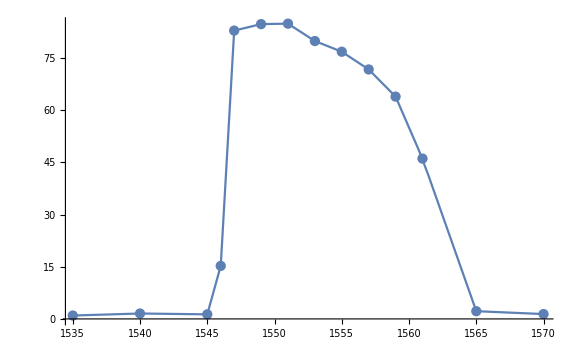

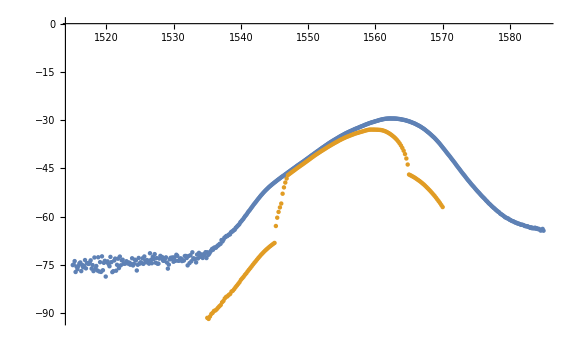

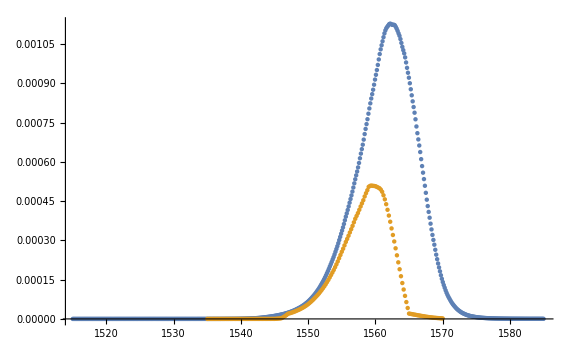

```mathematica
linterpolatedInputSpectrum= Interpolation[inputSpectrum,InterpolationOrder->1];
interpolatedVBG = Interpolation[VBG,InterpolationOrder->1];
reflectedSpectrummW = Table[{λ,dBmFrommW[mWFromdBm[linterpolatedInputSpectrum[λ]]×(Max[interpolatedVBG[λ],0]/100)]},
{λ, Max[Min[Max/@inputSpectrum[[All,1]]],Min[Max/@VBG[[All,1]]]],Min[Max[Max/@inputSpectrum[[All,1]]],Max[Max/@VBG[[All,1]]]], 0.2}];
reflectedSpectrumdB = Table[{λ,linterpolatedInputSpectrum[λ]+dBmFrommW[interpolatedVBG[λ]/100]},
{λ, Max[Min[Max/@inputSpectrum[[All,1]]],Min[Max/@VBG[[All,1]]]],Min[Max[Max/@inputSpectrum[[All,1]]],Max[Max/@VBG[[All,1]]]], 0.2}];
Show[
ListPlot[VBG, PlotRange-> Full],
Plot[interpolatedVBG[λ], {λ, Min[Max/@VBG],Max[Max/@VBG]}, PlotRange-> Full],
ImageSize->Large]
ListPlot[{
Table[{inputSpectrum[[i,1]], inputSpectrum[[i,2]]},{i, 1, Length[inputSpectrum]}],
Table[{reflectedSpectrummW[[i,1]], reflectedSpectrumdB[[i,2]]},{i, 1, Length[reflectedSpectrummW]}]
},ImageSize->Large]
ListPlot[{
Table[{inputSpectrum[[i,1]], mWFromdBm[inputSpectrum[[i,2]]]},{i, 1, Length[inputSpectrum]}],
Table[{reflectedSpectrumdB[[i,1]], mWFromdBm[reflectedSpectrummW[[i,2]]]},{i, 1, Length[reflectedSpectrumdB]}]
},ImageSize->Large]
```

```mathematica
(* Map - полезная штукат *)
```